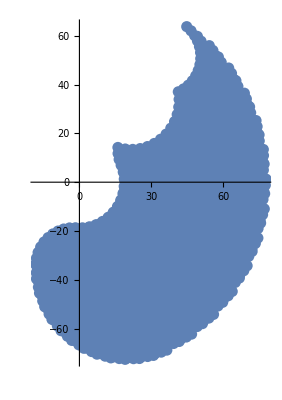

```mathematica
Module[{Lm,Lp,Ld,θm,θp,θd,Jm,Jp,T,x,y,workspace},(*Average lengths of the phalanges*)Lm=39.8;(*Length of the base phalanx*)Lp=22.4;(*Length of the middle phalanx*)Ld=15.8;(*Length of the tip phalanx*)(*List to store the workspace positions*)workspace={};
(*Iterate through all possible combinations of the three angles*)Do[(*Calculate joint positions*)Jm={Lm*Cos[θm],Lm*Sin[θm]};
Jp=Jm+{Lp*Cos[θm+θp],Lp*Sin[θm+θp]};
T=Jp+{Ld*Cos[θm+θp+θd],Ld*Sin[θm+θp+θd]};
(*Append fingertip position to the workspace list*)AppendTo[workspace,T],{θm,-Pi/3,Pi/3,Pi/20},{θp,-2Pi/3,0,Pi/20},{θd,-2Pi/3,0,Pi/20}];
(*Plot the workspace*)ListPlot[workspace,PlotStyle->PointSize[0.02],AspectRatio->Automatic]]
```

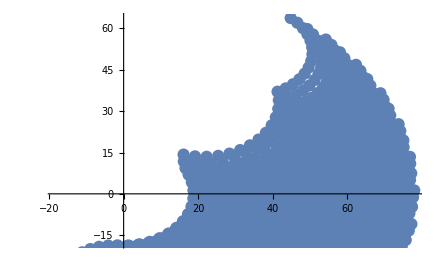

```mathematica
Module[{Lm,Lp,Ld,θm,θp,θd,Jm,Jp,T,x,y,workspace},(*Average lengths of the phalanges*)Lm=39.8;(*Length of the base phalanx*)Lp=22.4;(*Length of the middle phalanx*)Ld=15.8;(*Length of the tip phalanx*)(*List to store the workspace positions*)workspace={};
(*Iterate through all possible combinations of the three angles*)Do[(*Calculate joint positions*)Jm={Lm*Cos[θm],Lm*Sin[θm]};
Jp=Jm+{Lp*Cos[θm+θp],Lp*Sin[θm+θp]};
T=Jp+{Ld*Cos[θm+θp+θd],Ld*Sin[θm+θp+θd]};
(*Append fingertip position to the workspace list*)AppendTo[workspace,T],{θm,-Pi/3,Pi/3,Pi/20},{θp,-2Pi/3,0,Pi/20},{θd,-2Pi/3,0,Pi/20}];
(*Plot the workspace*)ListPlot[workspace,PlotStyle->PointSize[0.02],PlotRange->{{All,All},{-18,All}}]]
```